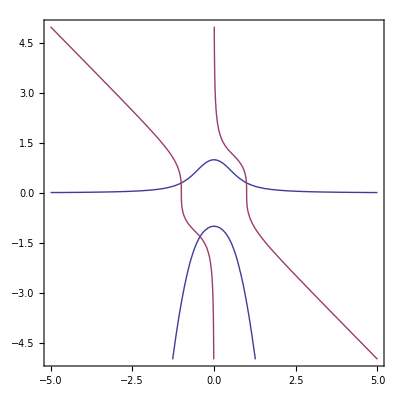

Jn != 0 True

Jn != 0 True

Jn != 0 True

«2 more identical outputs»

x1 = {-0.428033,-1.31189}

Jn != 0 True

Jn != 0 True

Jn != 0 True

«1 more identical outputs»

x2 = {0.99278,0.30644}

Jn != 0 True

Jn != 0 True

Jn != 0 True

x3 = {-1.00669,0.299428}

```mathematica
Clear[x];
Clear[y];
f=3 x^2 y +  y^2-1;
g = x^4+  x y^3-1;

ContourPlot[{f ==0, g == 0},{x,-5,5}, {y, -5,5}]

j=Det[({{D[f,x], D[f,y]}, {D[g,x], D[g,y]}})];

A=Det[({{f, D[f,y]}, {g, D[g,y]}})];
B=Det[({{D[f,x], f}, {D[g,x], g}})];
(*derF = D[f,x];
Print[D[derF,x]];
Print["derF= ",derF];
ckeckKantorovichTheorem[f_,segm_]:=(
Clear[x];
delta = Abs[segm[[2]]-segm[[1]]]/2;
x0=segm[[2]]-delta;
derF1=D[f,x];
derF2 = D[derF1,x]; 
x=x0;
Print["derF≠0 - ",derF1≠0];
B=Abs[1/derF1];
Print["B=",B];
η=Abs[f/derF1];
Print["η=",η];
Clear[x];
K=4 + 30*Max[Abs[segm[[1]]],Abs[segm[[2]]]];
Print["K=",K];
h = B K η;
Print["h = " , h];
Print[h≤1/2];
a = (1 - Sqrt[1 - 2 h])/h*η;
Print[a≤delta];
Return[x0];
);
*)
defineRoot[f_, startx_, endx_, starty_, endy_] := (
Clear[x];
Clear[y];
deltax = (endx-startx)/2;
x00=endx-deltax;
deltay = (endy-starty)/2;
y00=endy-deltay;
yn = y00;
xn = x00;
While[Abs[xn - x00] > 0.5 * 10^(-4)&& Abs[yn - y00] > 0.5 * 10^(-4) || xn == x00, 
	Clear[x];
Clear[y];
         x00 = xn;
          x = x00;
         y00 = yn;
          y = y00;
Print["Jn != 0 ",j != 0 ];
	xn = x00 - A/j;
yn = y00 - B/j;
         
];
Return[{xn, yn}];
);
Clear[x];
Clear[y];
x1 = defineRoot[f, -2, -0.1, -2,-1];
Print["x1 = ", x1];
Clear[x];
Clear[y];
x2 = defineRoot[f, 0.5, 2,0.01,1];
Print["x2 = ", x2];
Clear[x];
Clear[y];
x3 = defineRoot[f, -2, -0.1,0.01,1];
Print["x3 = ", x3];
```

```mathematica
(*defineRoot2[f_, start_, end_] := (
Clear[x];
x01 = start;
x02 = end;
xn = x01;
While[Abs[xn - x01] > 0.5 * 10^(-3) || xn == x01, 
	
          x = x01;
          fx01 = f;
	x = x02;
	fx02 = f;
	
	xn = x02  - ((x02-x01)fx02)/(fx02 - fx01);
	x01 = x02;
         x02 = xn;         
];
Return[xn];
);
Clear[x];
x1 = defineRoot2[f,-1.5, 0.5];
Print["x1 = ", x1];
Clear[x];
x2 = defineRoot2[f, -3, -1.5];
Print["x2 = ", x2];
Clear[x];
x3 = defineRoot2[f, 0.5, 3];
Print["x3 = ", x3];*)
```

x1 = -0.4

x2 = -1.73205

x3 = 1.73205